## Brownian motion and statistics of chains

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]]
```

## 1D Brownian Particle

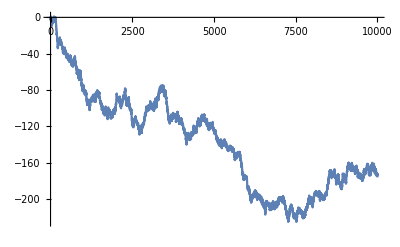

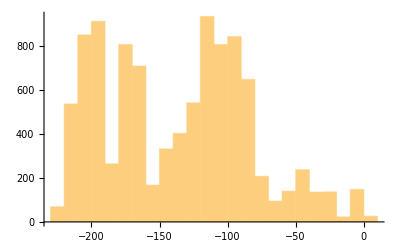

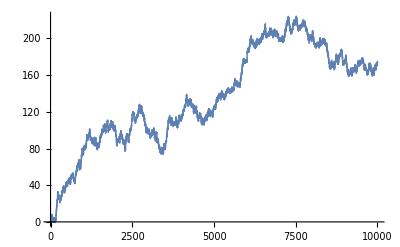

```mathematica
nstep=10000;
data=Accumulate[RandomInteger[{-1,1},nstep]];
ListLinePlot[%]
Histogram[data]
dist=Table[{i,Abs[data[[1]]-data[[i]]]},{i,Length@data}];
ListPlot[dist]
```

## 2D Brownian Particle

```mathematica
step=0.5;
Manipulate[Graphics[Line[Accumulate[step*RandomChoice[{-1,1},{n,2}]]],PlotRange->100],{n,10,10000,10}]
```

## 3D Brownian Particle

```mathematica
Manipulate[Graphics3D[Line[Accumulate[RandomChoice[{-1,1},{n,3}]]],PlotRange->100],{n,10,3000,10}]
```

```mathematica
Graphics3D[Line[Accumulate[RandomChoice[{-1,1},{10000,3}]]],PlotRange->100]
Export["b3D.jpeg",%]
```

-Graphics3D-

b3D.jpeg

### 3D MSD

3D random walk with the step a=1 is simulated. The distance between the beginning and the end is calculated and plotted as a 
function of the number of steps.

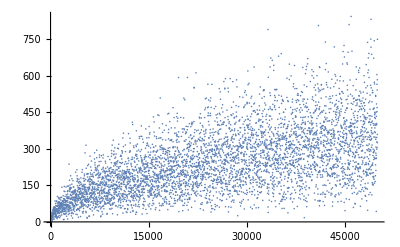

```mathematica
distance[a_]:=EuclideanDistance[a[[1]],a[[Length@a]]]

d=Table[{n,distance[Accumulate[RandomChoice[{-1,1},{n,3}]]]},{n,10,50000,10}];
pl1=ListPlot[%]
```

### Fitting the data

The results of simulations are fitted to the function 
			A* N^0.5
with A being a fitting parameter. This result is then compared to the theoretical prediction 
			A = √3

{a→1.6021}

1.6021 x^0.5

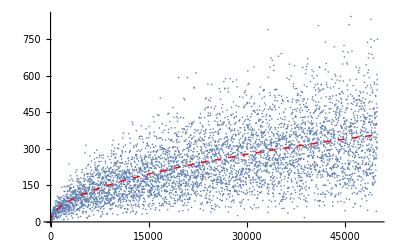

```mathematica
f=FindFit[d,a*x^0.5,{a},x]
fit=a*x^0.5/.f
Show[pl1,Plot[fit,{x,0,50000},PlotStyle->{Red,Dashed,Thick}]]
```

### Diffusion constant

The step is equal to a=1 in this simulation. Therefore, the RMSD should be given as
				rmsd = √(3 Na^2)=√(3N)

```mathematica
Sqrt[3.]
```

1.73205

## Distribution of end-to-end distances

### 2D

(ⅇ^(-r^2/(2 σ^2)) r)/σ^2

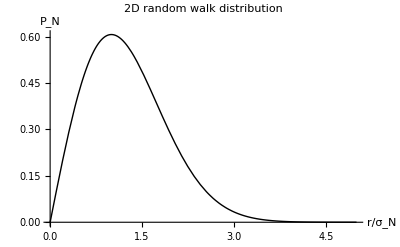

<r> = √(π/2) σ

<r^2> = 2 σ^2

```mathematica
g2[r_,σ_]=r/σ^2*Exp[-r^2/(2σ^2)]
Plot[g2[r,1],{r,0,5},PlotStyle->{Black,Thick},AxesLabel->{" r/σ_N "," P_N"},PlotLabel->" 2D random walk distribution "]
Print["  <r> = ",Integrate[r*g2[r,σ],{r,0,∞},Assumptions->{σ>0}]]
Print["  <r^2> = ",Integrate[r^2*g2[r,σ],{r,0,∞},Assumptions->{σ>0}]]
```

### 3D

(ⅇ^(-r^2/(2 σ^2)) √(2/π) r^2)/((σ^2)^(3/2))

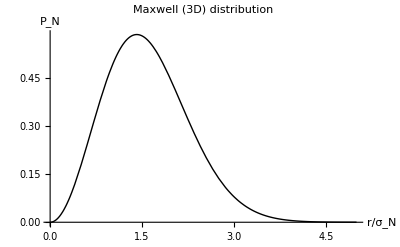

<r> = 2 √(2/π) σ

<r^2> = 3 σ^2

```mathematica
g3[r_,σ_]=4*π*r^2/(2*π*σ^2)^(3/2)*Exp[-r^2/(2σ^2)]
Plot[g3[r,1],{r,0,5},PlotStyle->{Black,Thick},AxesLabel->{" r/σ_N "," P_N"},PlotLabel->" Maxwell (3D) distribution"]
Print["  <r> = ",Integrate[r*g3[r,σ],{r,0,∞},Assumptions->{σ>0}]]
Print["  <r^2> = ",Integrate[r^2*g3[r,σ],{r,0,∞},Assumptions->{σ>0}]]
```